# Technical Prelim-1

```mathematica
Plot
Table
Manipulate
```

## Plotting using Plot Function

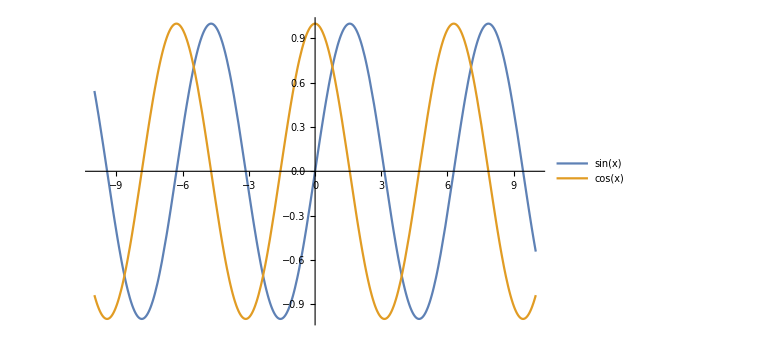

```mathematica
Plot[{Sin[x],Cos[x]},{x,-10,10}, ImageSize->Large, PlotLegends->"Expressions"]
```

```mathematica
Table[n,{n,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Table[n!,{n,1,10}]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

```mathematica
Table[Sin[n Pi/2],{n,0,8}]
```

{0,1,0,-1,0,1,0,-1,0}

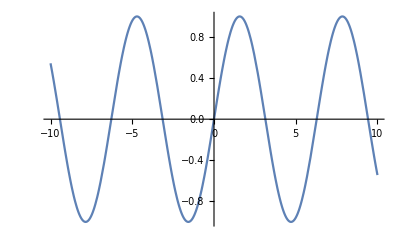
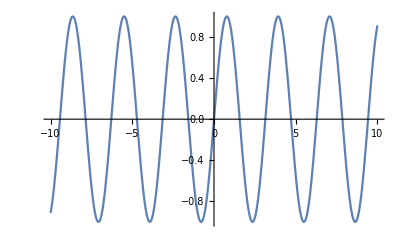
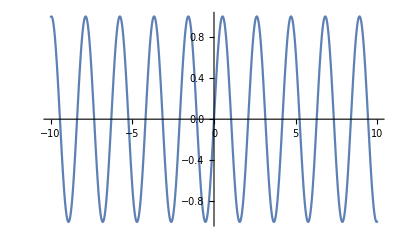
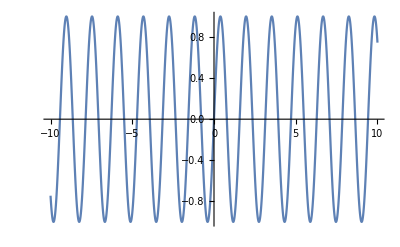

```mathematica
Table[Plot[Sin[n x],{x,-10,10}],{n,1,4}]
```

```mathematica
factorials = Table[Log[n!],{n,1,10}]
```

{0,Log[2],Log[6],Log[24],Log[120],Log[720],Log[5040],Log[40320],Log[362880],Log[3628800]}

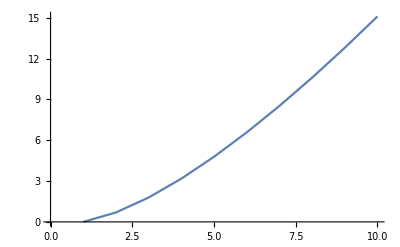

```mathematica
ListPlot[factorials,Joined->True]
```

```mathematica
{n^p, p^n, n!}
polynomials = Table[n^4, {n,1,10}]
```

{n^p,p^n,n!}

{1,16,81,256,625,1296,2401,4096,6561,10000}

```mathematica
exponentials = Table[4^n,{n,1,10}]
```

{4,16,64,256,1024,4096,16384,65536,262144,1048576}

```mathematica
factorials = Table[n!,{n,1,10}]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

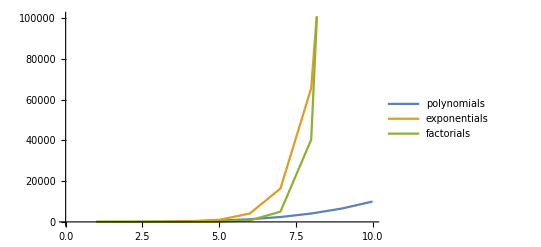

```mathematica
ListPlot[{polynomials,exponentials,factorials}, Joined->True, PlotLegends->{"polynomials","exponentials","factorials"}]
```

```mathematica
Manipulate[Plot[Sin[n x],{x, -10,10}],{{n,3},1,10}]
```